```mathematica
(*Inicialización de los parámetros de entrada, generación de vector aleatorio Z y del vector de covariables X a partir de éste*)
d=5;
n=10000;
Z=RandomVariate[NormalDistribution[],{n,d}];
D5=({{2, 0, 0, 0, 0}, {0, 5, 0, 0, 0}, {0, 0, 3, 0, 0}, {0, 0, 0, 3, 0}, {0, 0, 0, 0, 2}});
𝟙=Table[1,d];
X=Table[D5.Z[[i]]+d D5.𝟙,{i,1,n}];
```

```mathematica
(*Generación de parámetros a, b, p para cada individuo a partir de X*)
Xe=Table[Append[X[[i]],1],{i,1,n}];
{α,β,δ}=({{2, 1, 1, 0.5, 3, -30}, {3, 5, 4, 7, 4, -160}, {-0.2, -0.1, 0.2, 0.3, -0.2, -2.2}});
{a,b,c}={α,β,δ}.Transpose[Xe];
p=Table[ⅇ^c[[i]]/(1+ⅇ^c[[i]]),{i,1,n}];
```

```mathematica
(*Realización única de pérdida agregada S usando parámetros a, b, p*)
P=Table[RandomVariate[BernoulliDistribution[p[[i]]]],{i,1,n}];
B=Table[RandomVariate[GammaDistribution[a[[i]],b[[i]]]],{i,1,n}];
S=P.B
```

3.92332×10^7

```mathematica
(*Generación de muestra con m realizaciones de S*)
m=1000;
Zemp=RandomVariate[NormalDistribution[],{m n,d}];
Xemp=Table[D5.Zemp[[i]]+d D5.𝟙,{i,1,m n}];
Xeemp=Table[Append[Xemp[[i]],1],{i,1,m n}];
{aemp,bemp,cemp}={α,β,δ}.Transpose[Xeemp];
pemp=Table[ⅇ^cemp[[i]]/(1+ⅇ^cemp[[i]]),{i,1,m n}];
Pemp=Table[RandomVariate[BernoulliDistribution[pemp[[i]]]],{i,1,m n}];
Bemp=Table[RandomVariate[GammaDistribution[aemp[[i]],bemp[[i]]]],{i,1,m n}];
Semp=Table[Pemp[[i+1;;i+n]].Bemp[[i+1;;i+n]],{i,0,(m-1) n,n}];
```

```mathematica
(*Clustering*)
clust=ClusterClassify[X,3,Method->"KMeans"];
Ck=clust[X];
```

```mathematica
(*Estimación de parámetros a partir de clustering*)
πC=Table[Length[Cases[Ck,i]]/n,{i,1,Max[Ck]}];
qC=Table[Length[Cases[P Ck,i]]/(πC[[i]]n),{i,1,Max[Ck]}];
θC=Table[FindDistributionParameters[Extract[Position[P Ck,i]][B],GammaDistribution[AA,BB]],{i,1,Max[Ck]}];
```

```mathematica
(*Carga de parámetros estimados a partir de clustering en R*)
emp=Transpose[Import["~/Downloads/emp.csv"]][[2]][[2;;]];
πC=Transpose[Import["~/Downloads/p.csv"]][[2]][[2;;]];
qC=Transpose[Import["~/Downloads/q.csv"]][[2]][[2;;]];
AC=Transpose[Import["~/Downloads/A.csv"]][[2]][[2;;]];
BC=Transpose[Import["~/Downloads/B.csv"]][[2]][[2;;]];
```

```mathematica
(*Generación de muestra con 500 realizaciones de S con clustering*)
GC=Transpose[Table[RandomVariate[BernoulliDistribution[qC[[i]]],500n],{i,1,Length[πC]}]]Transpose[Table[RandomVariate[GammaDistribution[AA,BB]/.θC[[i]],500n],{i,1,Length[πC]}]];
F=GC.πC;
SC=Table[Total[F[[i+1;;i+n]]],{i,0,499n,n}];
```

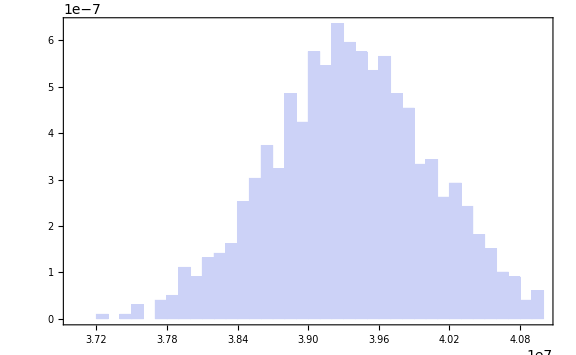
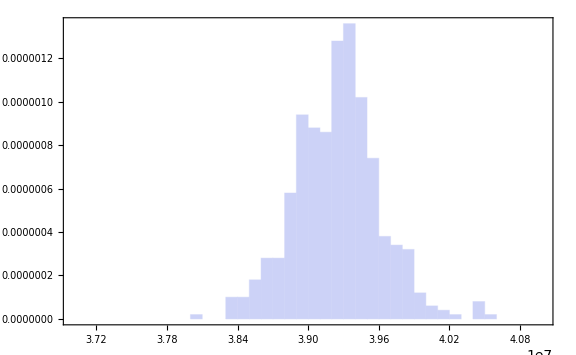

```mathematica
(*Generación de histogramas*)
Table[Histogram[Si,{37000000,41000000,100000},PDF,Frame->True,PlotTheme->"Classic",ImageSize->Large],{Si,{Semp,SC}}]
```

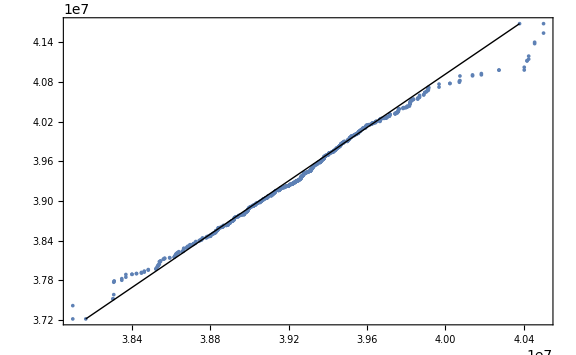

```mathematica
(*Generación de qq-plot*)
QuantilePlot[Semp,SC,ImageSize->Large]
```

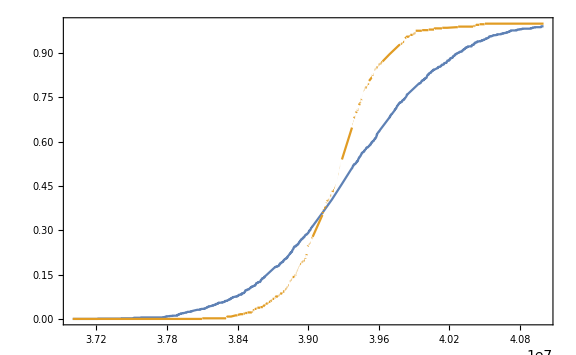

```mathematica
(*Comparación de FDAs*)
Plot[{CDF[EmpiricalDistribution[Semp],x],CDF[EmpiricalDistribution[SC],x]},{x,37000000,41000000},Frame->True,ImageSize->Large]
```